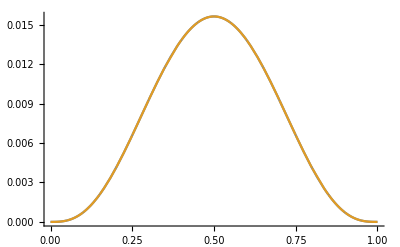

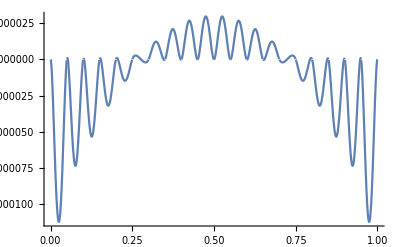

```mathematica
(* По зададено n пресмята кубичния сплайн Sn(t), интерполиращ функцията f(t)=t^3*(1-t)^3 в интервала [0,1] във възлите xk=k/n, k=0,...,n и такъв че Sn'(x0)=f'(x0) и Sn'(xn)=f'(xn) *)
(* Брой възли *)
n=20;
(* Функцията,която ще бъде интерполирана от кубичния сплайн *)
f[t_]:=t^3*(1-t)^3;
(* Инициализация на възлите *)
Do[x[k]=k/n,{k,0,n}];
(* Пресмятаме разстоянието между всеки 2 съседни възела. То ще бъде еднакво, защото са равноотдалечени. *)
delta=1/n;
(* Дефиниция на коефициентите в тридиагоналната матрица. Те ще бъдат еднакви за всяко i, защото разстоянията delta са равни. *)
a=1/delta;
b=4/delta;
c=1/delta;
(* Пресмятаме десните страни в тридиагоналната матрица *)
Do[r[k]=3*((f[x[k]]-f[x[k-1]])/(delta^2)+(f[x[k+1]]-f[x[k]])/(delta^2)),{k,1,n-1}];
(* Пълна кубична интерполация *)
d[0]=f'[x[0]];
d[n]=f'[x[n]];
(* Метод на прогонката - прав ход *)
alpha[1]=-c/b;
beta[1]=r[1]/b;
Do[{alpha[k]=-c/(a*alpha[k-1]+b),beta[k]=(r[k]-a*beta[k-1])/(a*alpha[k-1]+b)},{k,2,n-1}];
(* Метод на прогонката - обратен ход *)
Do[d[k]=alpha[k]*d[k+1]+beta[k],{k,n-1,1,-1}];
(* Общ вид на полиномите, интерполиращи f(t) във всеки подинтервал на [0,1], определен от два последователни интерполационни възела *)
Do[P[k,t_]=f[x[k]]+d[i](t-x[k])+(((f[x[k+1]]-f[x[k]])/delta-d[k])/delta)*((t-x[k])^2)+((d[k]+d[k+1]-2(f[x[k+1]]-f[x[k]])/delta)/(delta^2))*((t-x[k])^2)*(t-x[k+1]),{k,0,n-1}];
(* Конструиране на сплайна *)
Sn[t_]:=Sum[If[t≥x[i]&&t≤x[i+1],P[i,t],0],{i,0,n-1}];
(* Графики на функциите f(t) и Sn(t) в интервала [0,1] *)
Plot[{f[t],Sn[t]},{t,0,1},PlotRange->All]
(* Графика на f(t)-Sn(f;t) в интервала [0,1] - грешката *)
Plot[f[t]-Sn[t],{t,0,1},PlotRange->All]
```